# Triángulo de Sierpinski XXX

```mathematica
p[1]={1/2,√3/2};
p[2]={0,0};
p[3]={1,0};
V[0]={p[1],p[2],p[3]};
```

```mathematica
p1[1]={1/2};
p1[2]={0};
p1[3]={1};
F1[1][x_]:=1/2(x-p1[1])+p1[1]
F1[2][x_]:=1/2(x-p1[2])+p1[2]
F1[3][x_]:=1/2(x-p1[3])+p1[3]
```

```mathematica
F[1][x_]:=1/3(x-p[1])+p[1]
F[2][x_]:=1/3(x-p[2])+p[2]
F[3][x_]:=1/3(x-p[3])+p[3]
F[4][x_]:=1/3(x-(p[1]+p[2])/2)+(p[1]+p[2])/2
F[5][x_]:=1/3(x-(p[1]+p[3])/2)+(p[1]+p[3])/2
F[6][x_]:=1/3(x-(p[3]+p[2])/2)+(p[3]+p[2])/2
```

```mathematica
Simplify[F[4][p[2]]]
```

{1/6,1/(2 √3)}

```mathematica
V[1]=Union[F[1]/@V[0],F[2]/@V[0],F[3]/@V[0],F[4]/@V[0],F[5]/@V[0],F[6]/@V[0]];
V[m_]:=V[m]=Union[F[1]/@V[m-1],F[2]/@V[m-1],F[3]/@V[m-1],F[4]/@V[m-1],F[5]/@V[m-1],F[6]/@V[m-1]]
```

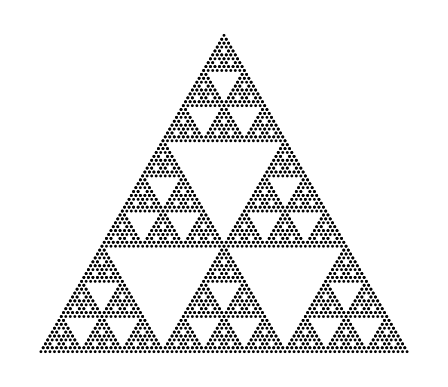

```mathematica
ListPlot[V[4],Axes->False,AspectRatio->√3/2,BaseStyle->Black]
```

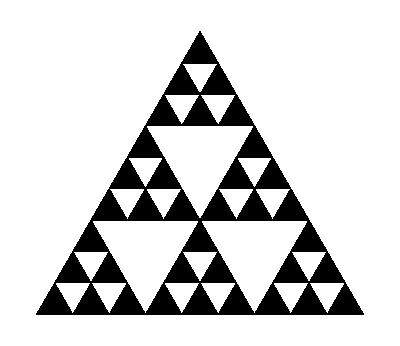

```mathematica
M1[{a_,b_,c_}]:={a,b,c}/.{a,b,c}-> {a,(2a+b)/3,(2a+c)/3}
M2[{a_,b_,c_}]:={a,b,c}/.{a,b,c}-> {(2a+b)/3,(a+2b)/3,(a+c+b)/3}
M3[{a_,b_,c_}]:={a,b,c}/.{a,b,c}-> {(2a+c)/3,(a+b+c)/3,(2c+a)/3}
M4[{a_,b_,c_}]:={a,b,c}/.{a,b,c}-> {(a+2b)/3,b,(c+2b)/3}
M5[{a_,b_,c_}]:={a,b,c}/.{a,b,c}-> {(c+a+b)/3,(2b+c)/3,(b+2c)/3}
M6[{a_,b_,c_}]:={a,b,c}/.{a,b,c}-> {(a+2c)/3,(b+2c)/3,c}
Vpol[0]=Polygon[V[0]];
Vpol[n_]:=Vpol[n-1]/.Polygon[{a_,b_,c_}]-> {Polygon[M1[{a,b,c}]],Polygon[M2[{a,b,c}]],Polygon[M3[{a,b,c}]],Polygon[M4[{a,b,c}]],Polygon[M5[{a,b,c}]],Polygon[M6[{a,b,c}]]}
Graphics[Vpol[2],BaseStyle->Black]
```

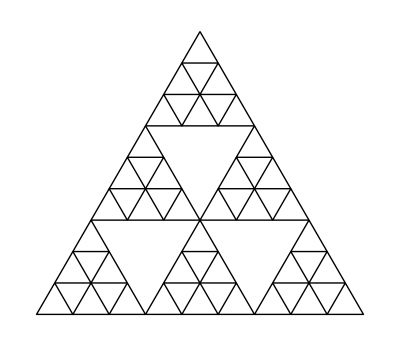

```mathematica
Ml1[{a_,b_,c_,a_}]:={a,b,c,a}/.{a,b,c,a}-> {a,(2a+b)/3,(2a+c)/3,a}
Ml2[{a_,b_,c_,a_}]:={a,b,c,a}/.{a,b,c,a}-> {(2a+b)/3,(a+2b)/3,(a+c+b)/3,(2a+b)/3}
Ml3[{a_,b_,c_,a_}]:={a,b,c,a}/.{a,b,c,a}-> {(2a+c)/3,(a+b+c)/3,(2c+a)/3,(2a+c)/3}
Ml4[{a_,b_,c_,a_}]:={a,b,c,a}/.{a,b,c,a}-> {(a+2b)/3,b,(c+2b)/3,(a+2b)/3}
Ml5[{a_,b_,c_,a_}]:={a,b,c,a}/.{a,b,c,a}-> {(c+a+b)/3,(2b+c)/3,(b+2c)/3,(c+a+b)/3}
Ml6[{a_,b_,c_,a_}]:={a,b,c,a}/.{a,b,c,a}-> {(a+2c)/3,(b+2c)/3,c,(a+2c)/3}

Vline[0]=Line[{p[1],p[2],p[3],p[1]}];
Vline[n_]:=Vline[n-1]/.Line[{a_,b_,c_,a_}]-> {Line[Ml1[{a,b,c,a}]],Line[Ml2[{a,b,c,a}]],Line[Ml3[{a,b,c,a}]],Line[Ml4[{a,b,c,a}]],Line[Ml5[{a,b,c,a}]],Line[Ml6[{a,b,c,a}]]}
Graphics[Vline[2],BaseStyle->Blue]
```

```mathematica
Show[Graphics[Vline[2]],Graphics[Text["a",{0,0},{0,1}, BaseStyle->{FontSize->24,FontFamily->"Bradley Hand",FontColor->Red,FontSlant->Italic}]],Graphics[Text["b",{1/2,0},{0,1}, BaseStyle->{FontSize->24,FontFamily->"Bradley Hand",FontColor->Red,FontSlant->Italic}]],Graphics[Text["c",{1,0},{0,1}, BaseStyle->{FontSize->24,FontFamily->"Bradley Hand",FontColor->Red,FontSlant->Italic}]],Graphics[Text["x",{1/4,0},{0,1},  BaseStyle->{FontSize->18,FontFamily->"Bradley Hand",FontColor->Blue,FontSlant->Italic}]],Graphics[Text["y",{3/4,0},{0,1}, BaseStyle->{FontSize->18,FontFamily->"Bradley Hand",FontColor->Blue,FontSlant->Italic}]],

Graphics[Text["t",{1/2,√3/2},{0,-1}, BaseStyle->{FontSize->24,FontFamily->"Bradley Hand",FontColor->Green,FontSlant->Italic}]],

Graphics[{PointSize[.025],Point[{0,0}]}],Graphics[{PointSize[.025],Point[{1/2,0}]}],Graphics[{PointSize[.025],Point[{1,0}]}],Graphics[{PointSize[.025],Point[{1/4,0}]}],Graphics[{PointSize[.025],Point[{3/4,0}]}],Graphics[{PointSize[.025],Point[{1/2,√3/2}]}],

Graphics[{PointSize[.025],Point[{#}]}]&[ V[2]]


]
```

-Graphics-

```mathematica
Show[Graphics[Vline[#]],Graphics[{PointSize[.025],Red,Point[{#}]}]&[ V[#]]]&[3]
```

-Graphics-

```mathematica
P[n_]:=Tuples[{F[1],F[2],F[3]},n];
```

```mathematica
P[3]
```

```mathematica
{{F[1],F[1],F[1]},{F[1],F[1],F[2]},{F[1],F[1],F[3]},{F[1],F[2],F[1]},{F[1],F[2],F[2]},{F[1],F[2],F[3]},{F[1],F[3],F[1]},{F[1],F[3],F[2]},{F[1],F[3],F[3]},{F[2],F[1],F[1]},{F[2],F[1],F[2]},{F[2],F[1],F[3]},{F[2],F[2],F[1]},{F[2],F[2],F[2]},{F[2],F[2],F[3]},{F[2],F[3],F[1]},{F[2],F[3],F[2]},{F[2],F[3],F[3]},{F[3],F[1],F[1]},{F[3],F[1],F[2]},{F[3],F[1],F[3]},{F[3],F[2],F[1]},{F[3],F[2],F[2]},{F[3],F[2],F[3]},{F[3],F[3],F[1]},{F[3],F[3],F[2]},{F[3],F[3],F[3]}}
```

{{F[1],F[1],F[1]},{F[1],F[1],F[2]},{F[1],F[1],F[3]},{F[1],F[2],F[1]},{F[1],F[2],F[2]},{F[1],F[2],F[3]},{F[1],F[3],F[1]},{F[1],F[3],F[2]},{F[1],F[3],F[3]},{F[2],F[1],F[1]},{F[2],F[1],F[2]},{F[2],F[1],F[3]},{F[2],F[2],F[1]},{F[2],F[2],F[2]},{F[2],F[2],F[3]},{F[2],F[3],F[1]},{F[2],F[3],F[2]},{F[2],F[3],F[3]},{F[3],F[1],F[1]},{F[3],F[1],F[2]},{F[3],F[1],F[3]},{F[3],F[2],F[1]},{F[3],F[2],F[2]},{F[3],F[2],F[3]},{F[3],F[3],F[1]},{F[3],F[3],F[2]},{F[3],F[3],F[3]}}

```mathematica
Composition[Sequence@@P[3][[3]]][p[2]]
```

{14/27,-1/(6 √3)+(√3)/2}

```mathematica
Composition[P[2]][p[1]]
```

{{F[1],F[1]},{F[1],F[2]},{F[1],F[3]},{F[2],F[1]},{F[2],F[2]},{F[2],F[3]},{F[3],F[1]},{F[3],F[2]},{F[3],F[3]}}[{1/2,(√3)/2}]

```mathematica
Ite[3]
```

Ite[3]

```mathematica
Composition[F[1],F[2],F[2]][p[2]]
```

{1/3,-1/(2 √3)+(√3)/2}

```mathematica
Composition[F[2],F[1],F[1]][p[1]]
```

{1/6,1/(2 √3)}

```mathematica
IteracionS[l_]:=Module[{lista=l,ult=Last[l]},While[lista≠{} &&lista[[-1]]==ult , lista=Delete[lista,-1]];Return[Length[lista]]]
IteracionS[{2}]
```

0

```mathematica
OrigenS[l_]:=Module[{lista=l,ult=Last[l]},While[lista≠{} &&lista[[-1]]==ult , lista=Delete[lista,-1]];lista=Append[lista,ult];Return[lista]]
```

```mathematica
OrigenS[{4,3,3,3}]
```

{4,3}

```mathematica
ultimosdos[w_List]:=Module[{lista=OrigenS[w]},While[Length[lista]>2,lista=Drop[lista,1]];Return[lista]]
```

```mathematica
ultimosdos[{3,3,3,3,3,2}]
```

{3,2}

```mathematica
AlternoS[w_List]:=Module[{lista=Composition[ultimosdos,OrigenS][w],lista2,lista3,ax,ult3},
If[Length[lista]<2,lista3=w];

If[Length[lista]≥ 2,

ax=Which[
lista=={1,2},{4,1},
lista=={4,1},{1,2},

lista=={2,1},{4,2},
lista=={4,2},{2,1},

lista=={1,3},{5,1},
lista=={5,1},{1,3},

lista=={3,1},{5,3},
lista=={5,3},{3,1},

lista=={2,3},{6,2},
lista=={6,2},{2,3},

lista=={3,2},{6,3},
lista=={6,3},{3,2}];
lista2=Drop[OrigenS[w],{-2,-1}];
lista3=Flatten[Append[lista2,ax]];
ult3=Last[lista3];
While[Length[lista3]<Length[w],lista3=Append[lista3,ult3]]

]; Return[lista3]]
```

```mathematica
AlternoS[{3,2}]
```

{6,3}

Indentifica las coordenadas de un punto dada una palabra

```mathematica
PuntoS[k_List]:=Return[For[j=Length[k]-1;q={},j>0,j--,r=F[k[[j]]];q=Append[q,r]];Composition[Sequence@@Reverse[q]][p[k[[Length[k]]]]]]
```

```mathematica
xj={6,1,4,3,2,1};
Simplify[PuntoS[xj]]
```

{119/243,32/(81 √3)}

```mathematica
IgualesS[k1_List,k2_List]:=Module[{w1=k1,w2=k2,x,ult1=Last[k1],ult2=Last[k2],l=Max[Length[k1],Length[k2]]},If[w1=={} || w2=={},x="Una palabra es vacia"];If[w1≠{} && w2≠{},While[Length[w1]<l,w1=Append[w1,ult1]];While[Length[w2]<l,w2=Append[w2,ult2]];If[w1==w2||AlternoS[w1]==w2,x="True"];
If[w1≠w2&&AlternoS[w1]≠w2,x="False"]];Return[x]]
```

```mathematica
IgualesS[{3,4,1,1},{3,1,2,2,2,2,2,2}]
```

True

```mathematica
abc[w_][v_]:=Module[{q=Flatten[Append[Drop[OrigenS[w],{-2,-1}],v]],ult},ult=Last[q];While[Length[q]<Length[w],q=Append[q,ult]];Return[q]]
```

```mathematica
Orden[w_]:=Module[{q1=Composition[ultimosdos,OrigenS][w],q2=Composition[ultimosdos,OrigenS,AlternoS][w]},

If[MemberQ[q1,3,5]==False&&MemberQ[q1,6]==False&&MemberQ[q2,3,5]==False&&MemberQ[q2,6]==False&&MemberQ[q1,1] && MemberQ[q2,1],Return[Flatten[{{abc[w][{1,1}]},{abc[w][{2,2}]},{abc[w][{3,3}]}},1] ]];

If[MemberQ[q1,3,5]==False&&MemberQ[q1,6]==False&&MemberQ[q2,3,5]==False&&MemberQ[q2,6]==False&& MemberQ[q1,2] && MemberQ[q2,2],Return[Flatten[{{abc[w][{2,2}]},{abc[w][{1,1}]},{abc[w][{3,3}]}},1 ]]];


If[MemberQ[q1,1,4]==False && MemberQ[q1,5]==False&&MemberQ[q2,1,4]==False && MemberQ[q2,5]==False&& MemberQ[q1,2] && MemberQ[q2,2],Return[Flatten[{{abc[w][{2,2}]},{abc[w][{3,3}]},{abc[w][{1,1}]}},1] ]];

If[MemberQ[q1,1,4]==False && MemberQ[q1,5]==False&&MemberQ[q2,1,4]==False && MemberQ[q2,5]==False&& MemberQ[q1,3] && MemberQ[q2,3],Return[Flatten[{{abc[w][{3,3}]},{abc[w][{2,2}]},{abc[w][{1,1}]}},1 ]]];



If[MemberQ[q1,2,4]==False&&MemberQ[q1,6]==False&&MemberQ[q2,2,4]==False&&MemberQ[q2,6]==False&& MemberQ[q1,1] && MemberQ[q2,1],Return[Flatten[{{abc[w][{1,1}]},{abc[w][{3,3}]},{abc[w][{2,2}]}},1 ]]];

If[MemberQ[q1,2,4]==False&&MemberQ[q1,6]==False&& MemberQ[q2,2,4]==False&&MemberQ[q2,6]==False&&MemberQ[q1,3] && MemberQ[q2,3],Return[Flatten[{{abc[w][{3,3}]},{abc[w][{1,1}]},{abc[w][{2,2}]}} ,1]]]
]
```

```mathematica
Vcentral[w_List]:=Module[{q=Drop[OrigenS[w],{-2,-1}],q1,q2,q3},q1=Flatten[Append[q,{1,1}],1];q2=Flatten[Append[q,{2,2}],1];q3=Flatten[Append[q,{3,3}],1];
While[Length[q1]<Length[w],q1=Append[q1,1]];While[Length[q2]<Length[w],q2=Append[q2,2]];While[Length[q3]<Length[w],q3=Append[q3,3]];
Return[{q1,q2,q3}]]
```

```mathematica
Vcentral[{4,3,3}]
```

{{1,1,1},{2,2,2},{3,3,3}}

```mathematica
ArmonicaS[a_,b_,c_][w_List]:=ArmonicaS[a,b,c][w]=If[IteracionS[w]==0,Which[OrigenS[w]=={1},a,OrigenS[w]=={2},b,OrigenS[w]=={3},c],

If[Composition[ultimosdos,OrigenS][w]=={6,1}||Composition[ultimosdos,OrigenS][w]=={5,2}||Composition[ultimosdos,OrigenS][w]=={4,3},

Return[(ArmonicaS[a,b,c] [Flatten[Vcentral[w][[1]]]]+ArmonicaS[a,b,c] [Flatten[Vcentral[w][[2]]]]+ArmonicaS[a,b,c] [Flatten[Vcentral[w][[3]]]])/3],

Module[{xe=Orden[w]},Return[(8*ArmonicaS[a,b,c][Flatten[xe[[1]]]]+4*ArmonicaS[a,b,c][Flatten[xe[[2]]]]+3*ArmonicaS[a,b,c][Flatten[xe[[3]]]]
)/15]]]]
```

```mathematica
ArmonicaS[1,0,0][{2,5,1,3}]
```

617/3375

```mathematica
Orden[{2,5,1,3}]
```

{{2,5,1,1},{2,5,3,3},{2,5,2,2}}

```mathematica
ArmonicaS[1,0,0][{6,6,6,3}]
```

259/1125

```mathematica
PuntoArmonicaS[p1_,p2_,p3_][l_List]:=Append[PuntoS[l],ArmonicaS[p1,p2,p3][l]]
(*PuntoArmonicaS1[p1_,p2_,p3_][l_List]:={PuntoArmonicaS[p1,p2,p3][l][[1]],PuntoArmonicaS[p1,p2,p3][l][[2]],PuntoArmonicaS[p1,p2,p3][l][[3]]}*)

PalabrapuntoS[w_List]:={Append[w,1],Append[w,2],Append[w,3]}
PalabrasS[n_]:=Flatten[PalabrapuntoS/@Tuples[{1,2,3,4,5,6},n],1]

CeldasS[a_,b_,c_][n_]:=CeldasS[a,b,c][n]=PuntoArmonicaS[a,b,c]/@PalabrasS[n]
```

```mathematica
PuntoArmonicaSS[p1_,p2_,p3_][l_List]:=Append[PuntoS[l],ArmonicaS[p1,p2,p3][l]]
PuntoArmonicaSS1[p1_,p2_,p3_][l_List]:={PuntoArmonicaSS[p1,p2,p3][l[[1]]],PuntoArmonicaSS[p1,p2,p3][l[[2]]],PuntoArmonicaSS[p1,p2,p3][l[[3]]]}
PalabrapuntoSS[w_List]:={Append[w,1],Append[w,2],Append[w,3]}
PalabrasSS[n_]:=PalabrapuntoSS/@ Tuples[{1,2,3,4,5,6},n]
CeldasSS[a_,b_,c_][n_]:=CeldasSS[a,b,c][n]=PuntoArmonicaSS1[a,b,c]/@PalabrasSS[n]
```

```mathematica
Simplify[PuntoArmonicaSS[1,0,0][{2,1,3}]]
```

{2/9,1/(3 √3),44/225}

```mathematica
AlternoS[{3,5,1}]
```

{3,1,3}

```mathematica
Orden[{2,1,3}]
```

{{2,1,1},{2,3,3},{2,2,2}}

```mathematica
Orden[{2,5,1}]
```

{{2,1,1},{2,3,3},{2,2,2}}

```mathematica
Simplify[PuntoArmonicaSS[1,0,0][{2,5,1}]](*PROBLEMA*)
```

{2/9,1/(3 √3),44/225}

```mathematica
Simplify[PuntoArmonicaSS[1,0,0][{3,1,3}]]
```

{8/9,1/(3 √3),41/225}

```mathematica
Simplify[PuntoArmonicaSS[1,0,0][{3,5,1}]]
```

{8/9,1/(3 √3),41/225}

```mathematica
Graphics3D[Polygon/@CeldasSS[1,0,0][3]]
```

-Graphics3D-

```mathematica
ListPlot3D[CeldasSS[1,0,0][3],ColorFunction->"TemperatureMap",AspectRatio->2/√3]
```

-Graphics3D-

```mathematica
Opuesto[w_List]:=Module[{j=Drop[w,-1],ult,pen},If[Length[w]≥ 2,ult=Last[w];pen=w[[-2]];ReplacePart[j,-1-> Abs[ult-pen]],w]]
```

```mathematica
Anadir[w_]:=Append[w,{2,3}]
PalabrasBottom[n_]:=Anadir/@Tuples[{2,3},n]
TotalPalabrasBottom[n_]:=DeleteDuplicates[Partition[Flatten[{PalabrasBottom[n-1],Table[2,n+1],Table[3,n+1]}],n+1]]
```

```mathematica
TotalPalabrasBottom[2]
```

{{2,2,3},{3,2,3},{2,2,2},{3,3,3}}

```mathematica
ArmonicaB[a_,b_,c_][w_]:=Module[{t=(5*b-2*a-2*c)},Armonica[t,a,c][w]]
```

```mathematica
ArmonicaB[0,(1/5),1][{2,2,2,3}]
```

Armonica[-1,0,1][{2,2,2,3}]

```mathematica
PuntoArmonicaB[p1_,p2_,p3_][l_List]:=Append[Punto1[l],ArmonicaB[p1,p2,p3][l]]
PuntoArmonicaB1[p1_,p2_,p3_][l_List]:={PuntoArmonicaB[p1,p2,p3][l[[1]]],PuntoArmonicaB[p1,p2,p3][l[[2]]]}
CeldasB[a_,b_,c_][n_]:=DeleteDuplicates[PuntoArmonicaB[a,b,c]/@Tuples[{2,3},n+1]]
```

```mathematica
Union[TotalPalabrasBottom[5],{{2,3}}]
```

{{2,3},{2,2,2,2,2,2},{2,2,2,2,2,3},{2,2,2,3,2,3},{2,2,3,2,2,3},{2,2,3,3,2,3},{2,3,2,2,2,3},{2,3,2,3,2,3},{2,3,3,2,2,3},{2,3,3,3,2,3},{3,2,2,2,2,3},{3,2,2,3,2,3},{3,2,3,2,2,3},{3,2,3,3,2,3},{3,3,2,2,2,3},{3,3,2,3,2,3},{3,3,3,2,2,3},{3,3,3,3,2,3},{3,3,3,3,3,3}}

```mathematica
ListCurvePathPlot[CeldasB[0,4/25,1][4]]
```

ListCurvePathPlot[{Punto1[{2,2,2,2,2},Armonica[-6/5,0,1][{2,2,2,2,2}]],Punto1[{2,2,2,2,3},Armonica[-6/5,0,1][{2,2,2,2,3}]],Punto1[{2,2,2,3,2},Armonica[-6/5,0,1][{2,2,2,3,2}]],Punto1[{2,2,2,3,3},Armonica[-6/5,0,1][{2,2,2,3,3}]],Punto1[{2,2,3,2,2},Armonica[-6/5,0,1][{2,2,3,2,2}]],Punto1[{2,2,3,2,3},Armonica[-6/5,0,1][{2,2,3,2,3}]],Punto1[{2,2,3,3,2},Armonica[-6/5,0,1][{2,2,3,3,2}]],Punto1[{2,2,3,3,3},Armonica[-6/5,0,1][{2,2,3,3,3}]],Punto1[{2,3,2,2,2},Armonica[-6/5,0,1][{2,3,2,2,2}]],Punto1[{2,3,2,2,3},Armonica[-6/5,0,1][{2,3,2,2,3}]],Punto1[{2,3,2,3,2},Armonica[-6/5,0,1][{2,3,2,3,2}]],Punto1[{2,3,2,3,3},Armonica[-6/5,0,1][{2,3,2,3,3}]],Punto1[{2,3,3,2,2},Armonica[-6/5,0,1][{2,3,3,2,2}]],Punto1[{2,3,3,2,3},Armonica[-6/5,0,1][{2,3,3,2,3}]],Punto1[{2,3,3,3,2},Armonica[-6/5,0,1][{2,3,3,3,2}]],Punto1[{2,3,3,3,3},Armonica[-6/5,0,1][{2,3,3,3,3}]],Punto1[{3,2,2,2,2},Armonica[-6/5,0,1][{3,2,2,2,2}]],Punto1[{3,2,2,2,3},Armonica[-6/5,0,1][{3,2,2,2,3}]],Punto1[{3,2,2,3,2},Armonica[-6/5,0,1][{3,2,2,3,2}]],Punto1[{3,2,2,3,3},Armonica[-6/5,0,1][{3,2,2,3,3}]],Punto1[{3,2,3,2,2},Armonica[-6/5,0,1][{3,2,3,2,2}]],Punto1[{3,2,3,2,3},Armonica[-6/5,0,1][{3,2,3,2,3}]],Punto1[{3,2,3,3,2},Armonica[-6/5,0,1][{3,2,3,3,2}]],Punto1[{3,2,3,3,3},Armonica[-6/5,0,1][{3,2,3,3,3}]],Punto1[{3,3,2,2,2},Armonica[-6/5,0,1][{3,3,2,2,2}]],Punto1[{3,3,2,2,3},Armonica[-6/5,0,1][{3,3,2,2,3}]],Punto1[{3,3,2,3,2},Armonica[-6/5,0,1][{3,3,2,3,2}]],Punto1[{3,3,2,3,3},Armonica[-6/5,0,1][{3,3,2,3,3}]],Punto1[{3,3,3,2,2},Armonica[-6/5,0,1][{3,3,3,2,2}]],Punto1[{3,3,3,2,3},Armonica[-6/5,0,1][{3,3,3,2,3}]],Punto1[{3,3,3,3,2},Armonica[-6/5,0,1][{3,3,3,3,2}]],Punto1[{3,3,3,3,3},Armonica[-6/5,0,1][{3,3,3,3,3}]]}]

```mathematica
PuntoArmonicaB[0,1/5,1][{3,2,3}]
```

Punto1[{3,2,3},Armonica[-1,0,1][{3,2,3}]]

```mathematica
AnadirSX[w_]:={Append[w,1],Append[w,2],Append[w,3]}
PalabrasSX[n_]:=AnadirSX/@Tuples[{1,2,3,4,5,6},n]
TotalPalabrasSX[n_]:=DeleteDuplicates[Partition[Flatten[{PalabrasSX[n],Table[2,n+1],Table[3,n+1]}],n+1]]
```